```mathematica
{hypgen1,hypgen10,hypgen50,hypgen90,hypgen99,hypkeep1,hypkeep10,hypkeep50,hypkeep90,hypkeep99,hypmem1,hypmem10,hypmem50,hypmem90,hypmem99,hypkill1,hypkill10,hypkill50,hypkill90,hypkill99,hyptyp1,hyptyp10,hyptyp50,hyptyp90,hyptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hyp500c24hpercent.mx"];
```

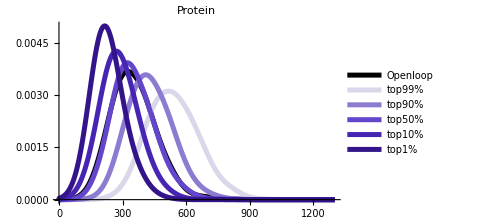

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hypgen1[[1]][[1]]/hypgen1[[1]][[6]],hypgen10[[1]][[1]]/hypgen10[[1]][[6]],hypgen50[[1]][[1]]/hypgen50[[1]][[6]],hypgen90[[1]][[1]]/hypgen90[[1]][[6]],hypgen99[[1]][[1]]/hypgen99[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.005}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#dad7ea"],Thickness[0.01]],Directive[RGBColor["#8c7bd1"],Thickness[0.01]],Directive[RGBColor["#6446cd"],Thickness[0.01]],Directive[RGBColor["#4725b3"],Thickness[0.01]],Directive[RGBColor["#33148a"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

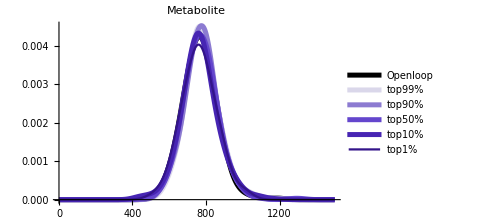

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hypgen1[[1]][[4]]/hypgen1[[1]][[6]],hypgen10[[1]][[4]]/hypgen10[[1]][[6]],hypgen50[[1]][[4]]/hypgen50[[1]][[6]],hypgen90[[1]][[4]]/hypgen90[[1]][[6]],hypgen99[[1]][[4]]/hypgen99[[1]][[6]]},40,PlotRange->{{0,1500},Automatic},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite",Black,16],
PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#dad7ea"],Thickness[0.01]],Directive[RGBColor["#8c7bd1"],Thickness[0.01]],Directive[RGBColor["#6446cd"],Thickness[0.01]],Directive[RGBColor["#4725b3"],Thickness[0.01]],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

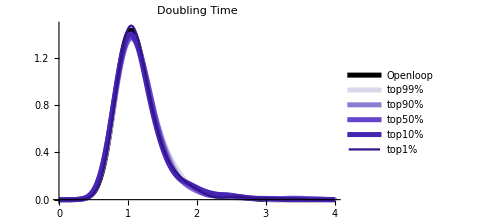

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hypgen1[[1]][[5]],Log[2]/hypgen10[[1]][[5]],Log[2]/hypgen50[[1]][[5]],Log[2]/hypgen90[[1]][[5]],Log[2]/hypgen99[[1]][[5]]},0.15,PlotRange->{{0,4},Automatic},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#dad7ea"],Thickness[0.01]],Directive[RGBColor["#8c7bd1"],Thickness[0.01]],Directive[RGBColor["#6446cd"],Thickness[0.01]],Directive[RGBColor["#4725b3"],Thickness[0.01]],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

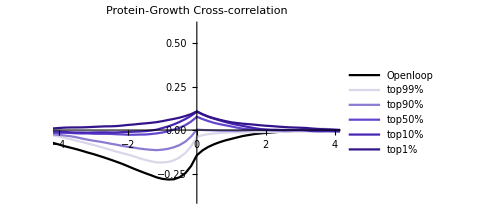

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hypmem1[[4]],hypmem10[[4]],hypmem50[[4]],hypmem90[[4]],hypmem99[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

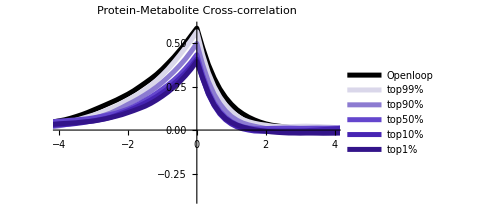

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hypmem1[[6]],hypmem10[[6]],hypmem50[[6]],hypmem90[[6]],hypmem99[[6]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#dad7ea"],Thickness[0.01]],Directive[RGBColor["#8c7bd1"],Thickness[0.01]],Directive[RGBColor["#6446cd"],Thickness[0.01]],Directive[RGBColor["#4725b3"],Thickness[0.01]],Directive[RGBColor["#33148a"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

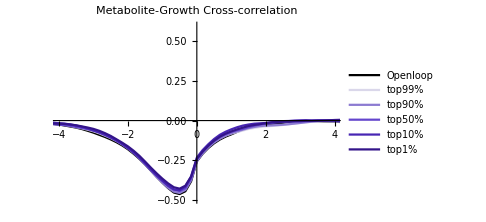

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hypmem1[[5]],hypmem10[[5]],hypmem50[[5]],hypmem90[[5]],hypmem99[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

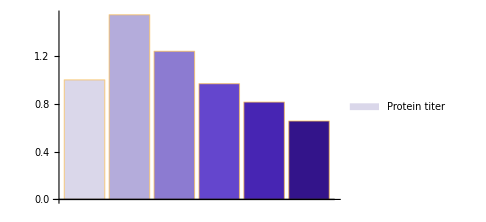

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hyptyp1[[2]]/oltyp[[2]],hyptyp10[[2]]/oltyp[[2]],hyptyp50[[2]]/oltyp[[2]],hyptyp90[[2]]/oltyp[[2]],hyptyp99[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

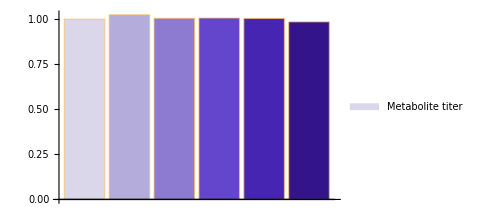

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hyptyp1[[4]]/oltyp[[4]],hyptyp10[[4]]/oltyp[[4]],hyptyp50[[4]]/oltyp[[4]],hyptyp90[[4]]/oltyp[[4]],hyptyp99[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite titer"},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

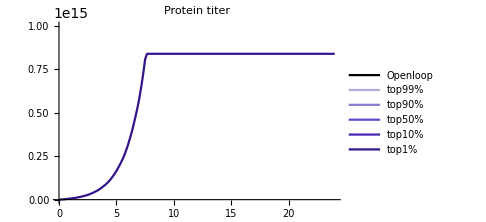

```mathematica
ListLinePlot[{oltyp[[1]],hyptyp1[[1]],hyptyp10[[1]],hyptyp50[[1]],hyptyp90[[1]],hyptyp99[[1]]},PlotLabel->"Protein titer",PlotStyle->{Black,
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium,PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"}]
```

```mathematica
ListLinePlot[{oltyp[[3]],hyptyp1[[3]],hyptyp10[[3]],hyptyp50[[3]],hyptyp90[[3]],hyptyp99[[3]]},PlotLabel->"metabolite titer",PlotStyle->{Directive[Black,Thickness[0.01]],
Directive[RGBColor["#b4acdb"],Thickness[0.01]],
Directive[RGBColor["#8c7bd1"],Thickness[0.01]],
Directive[RGBColor["#6446cd"],Thickness[0.01]],
Directive[RGBColor["#4725b3"],Thickness[0.01]],
Directive[RGBColor["#33148a"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-

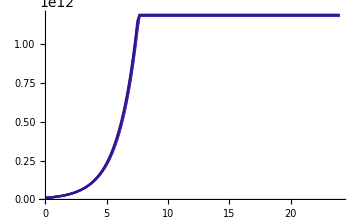

```mathematica
ListLinePlot[{Transpose@{ol500c24hkill[[All,1]],ol500c24hkill[[All,12]]},Transpose@{hypkill1[[All,1]],hypkill1[[All,12]]},Transpose@{hypkill10[[All,1]],hypkill10[[All,12]]},Transpose@{hypkill50[[All,1]],hypkill50[[All,12]]},Transpose@{hypkill90[[All,1]],hypkill90[[All,12]]},Transpose@{hypkill99[[All,1]],hypkill99[[All,12]]}},PlotStyle->{Black,
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium, Axes->{True,True}]
```